# Сигнальные созвездия

## APSK

Без шума

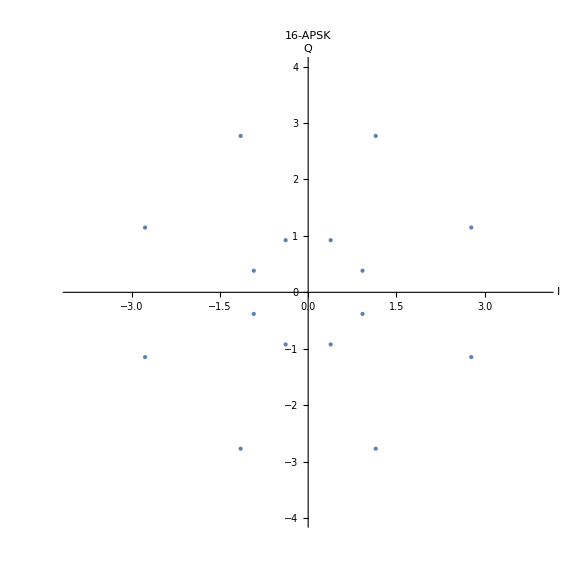

C:\Modulation\Constellation diagram\apsk16n0a0.jpg

```mathematica
apsk16n0a0=ListPlot[Flatten[Table[{N[k Cos[i 2π]],N[ k Sin[i 2 π]]},{k,1,3,2},{i,1/16,1,1/8}],1],PlotStyle->PointSize[Large],PlotRange->{{-4,4},{-4,4}},AspectRatio->1,PlotLabel->Style[Framed["16-APSK"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\apsk16n0a0.jpg",apsk16n0a0]
```

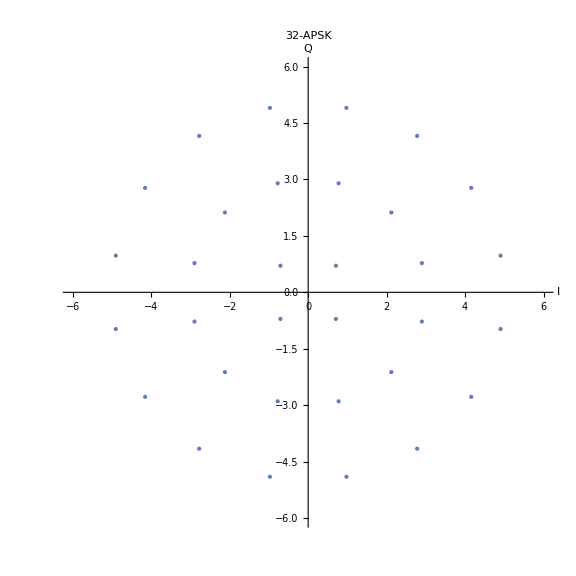

C:\Modulation\Constellation diagram\apsk32n0a0.jpg

```mathematica
apsk32n0a0=ListPlot[Flatten[{Table[{N[ Cos[i 2π]],N[ Sin[i 2 π]]},{i,1/8,1,1/4}],Table[{N[ 3Cos[i 2π]],N[3Sin[i 2 π]]},{i,1/24,1,1/12}],Table[{N[5Cos[i 2π]],N[5Sin[i 2 π]]},{i,1/32,1,1/16}]},1],PlotStyle->PointSize[Large],PlotRange->{{-6,6},{-6,6}},AspectRatio->1,PlotLabel->Style[Framed["32-APSK"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\apsk32n0a0.jpg",apsk32n0a0]
```

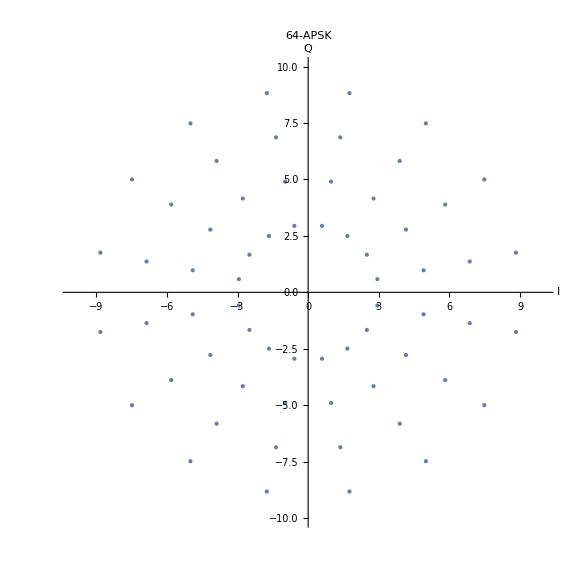

C:\Modulation\Constellation diagram\apsk64n0a0.jpg

```mathematica
apsk64n0a0=ListPlot[Flatten[Table[{N[k Cos[i 2π]],N[ k Sin[i 2 π]]},{k,3,9,2},{i,1/32,1,1/16}],1],PlotStyle->PointSize[Large],PlotRange->{{-10,10},{-10,10}},AspectRatio->1,PlotLabel->Style[Framed["64-APSK"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\apsk64n0a0.jpg",apsk64n0a0]
```

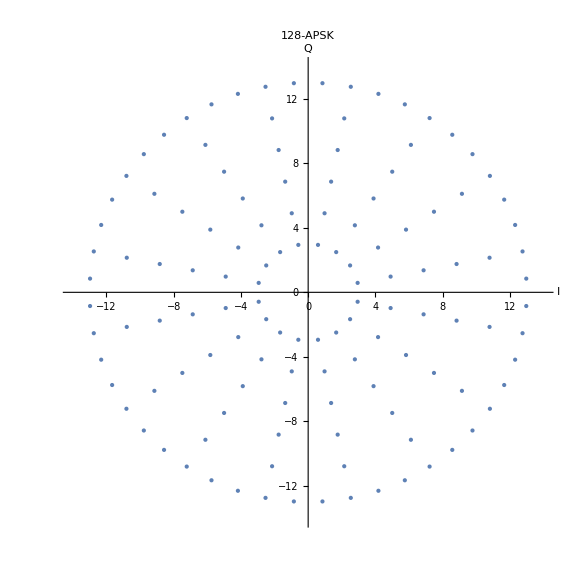

C:\Modulation\Constellation diagram\apsk128n0a0.jpg

```mathematica
apsk128n0a0=ListPlot[Flatten[{Flatten[Table[{N[ k Cos[i 2π]],N[k Sin[i 2 π]]},{k,3,11,2},{i,1/32,1,1/16}],1],Table[{N[13Cos[i 2π]],N[13Sin[i 2π]]},{i,1/96,1,1/48}]},1],PlotStyle->PointSize[Large],PlotRange->{{-14,14},{-14,14}},AspectRatio->1,PlotLabel->Style[Framed["128-APSK"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\apsk128n0a0.jpg",apsk128n0a0]
```

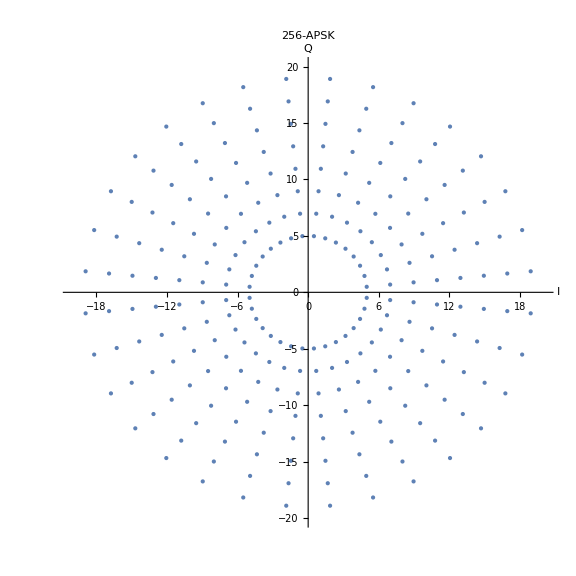

C:\Modulation\Constellation diagram\apsk256n0a0.jpg

```mathematica
apsk256n0a0=ListPlot[Flatten[Table[{N[k Cos[i 2π]],N[ k Sin[i 2 π]]},{k,5,19,2},{i,1/64,1,1/32}],1],PlotStyle->PointSize[Large],PlotRange->{{-20,20},{-20,20}},AspectRatio->1,PlotLabel->Style[Framed["256-APSK"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\apsk256n0a0.jpg",apsk256n0a0]
```

С шумом Δ∈{-0.1A, 0.1A}

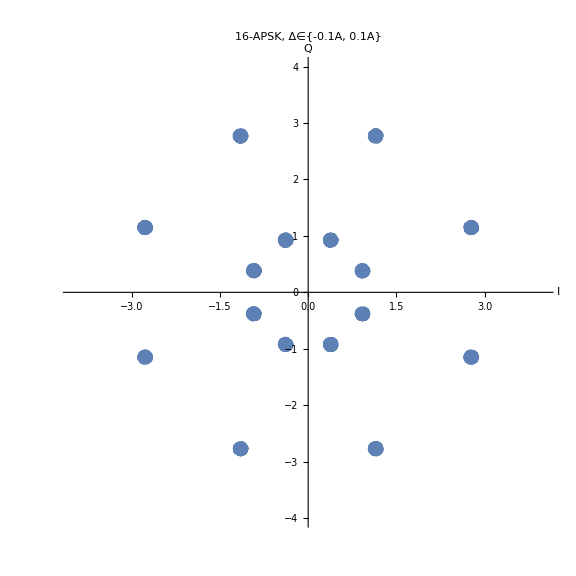

C:\Modulation\Constellation diagram\apsk16n1a0.jpg

```mathematica
apsk16n1a0=ListPlot[Transpose[Module[{n=16000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[Table[{N[k Cos[i 2π]],N[ k Sin[i 2 π]]},{k,1,3,2},{i,1/16,1,1/8}],1],n]];intdata=RandomReal[{-0.1,0.1},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-4,4},{-4,4}},AspectRatio->1,PlotLabel->Style[Framed["16-APSK, Δ∈{-0.1A, 0.1A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\apsk16n1a0.jpg",apsk16n1a0]
```

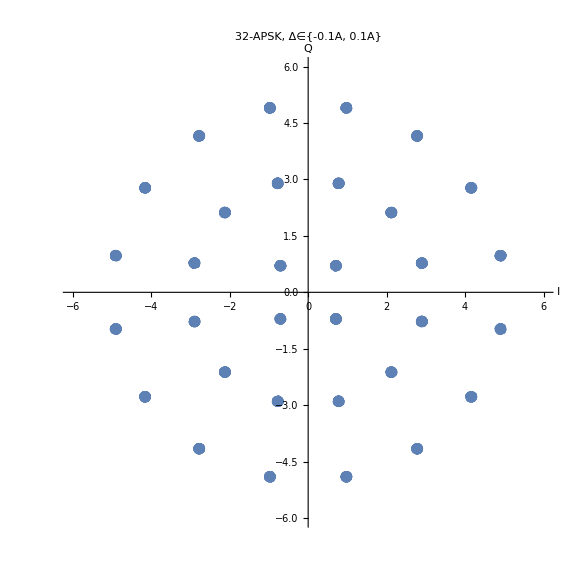

C:\Modulation\Constellation diagram\apsk32n1a0.jpg

```mathematica
apsk32n1a0=ListPlot[Transpose[Module[{n=32000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[{Table[{N[ Cos[i 2π]],N[ Sin[i 2 π]]},{i,1/8,1,1/4}],Table[{N[ 3Cos[i 2π]],N[3Sin[i 2 π]]},{i,1/24,1,1/12}],Table[{N[ 5Cos[i 2π]],N[5Sin[i 2 π]]},{i,1/32,1,1/16}]},1],n]];intdata=RandomReal[{-0.1,0.1},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-6,6},{-6,6}},AspectRatio->1,PlotLabel->Style[Framed["32-APSK, Δ∈{-0.1A, 0.1A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\apsk32n1a0.jpg",apsk32n1a0]
```

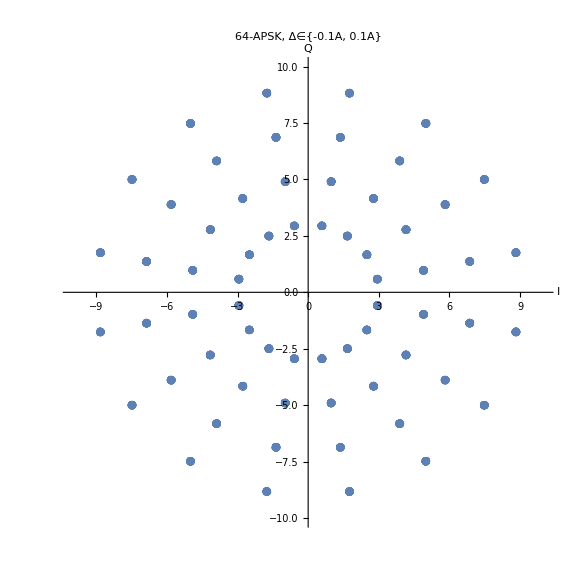

C:\Modulation\Constellation diagram\apsk64n1a0.jpg

```mathematica
apsk64n1a0=ListPlot[Transpose[Module[{n=64000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[Table[{N[ k Cos[i 2π]],N[ k Sin[i 2 π]]},{k,3,9,2},{i,1/32,1,1/16}],1],n]];intdata=RandomReal[{-0.1,0.1},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-10,10},{-10,10}},AspectRatio->1,PlotLabel->Style[Framed["64-APSK, Δ∈{-0.1A, 0.1A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\apsk64n1a0.jpg",apsk64n1a0]
```

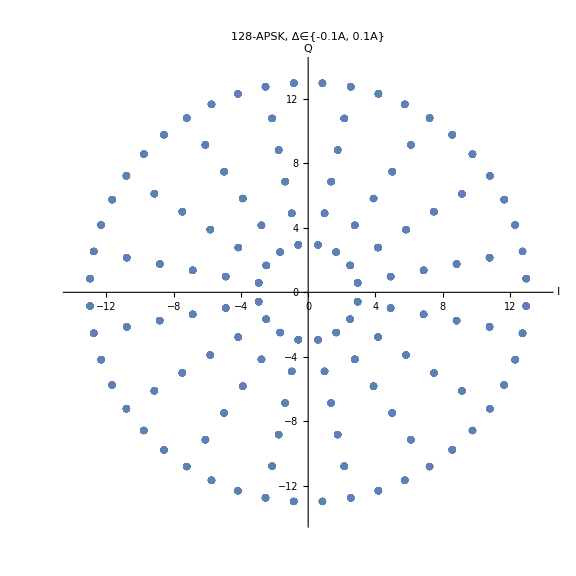

C:\Modulation\Constellation diagram\apsk128n1a0.jpg

```mathematica
apsk128n1a0=ListPlot[Transpose[Module[{n=128000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[{Flatten[Table[{N[k Cos[i 2π]],N[ k Sin[i 2 π]]},{k,3,11,2},{i,1/32,1,1/16}],1],Table[{N[13Cos[i 2π]],N[13Sin[i 2π]]},{i,1/96,1,1/48}]},1],n]];intdata=RandomReal[{-0.1,0.1},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-14,14},{-14,14}},AspectRatio->1,PlotLabel->Style[Framed["128-APSK, Δ∈{-0.1A, 0.1A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\apsk128n1a0.jpg",apsk128n1a0]
```

```mathematica
apsk256n1a0=ListPlot[Transpose[Module[{n=256000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[Table[{N[ k Cos[i 2π]],N[ k Sin[i 2 π]]},{k,5,19,2},{i,1/64,1,1/32}],1],n]];intdata=RandomReal[{-0.1,0.1},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-20,20},{-20,20}},AspectRatio->1,PlotLabel->Style[Framed["256-APSK, Δ∈{-0.1A, 0.1A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\apsk256n1a0.jpg",apsk256n1a0]
```

-Graphics-

C:\Modulation\Constellation diagram\apsk256n1a0.jpg

С шумом Δ∈{-0.25A, 0.25A}

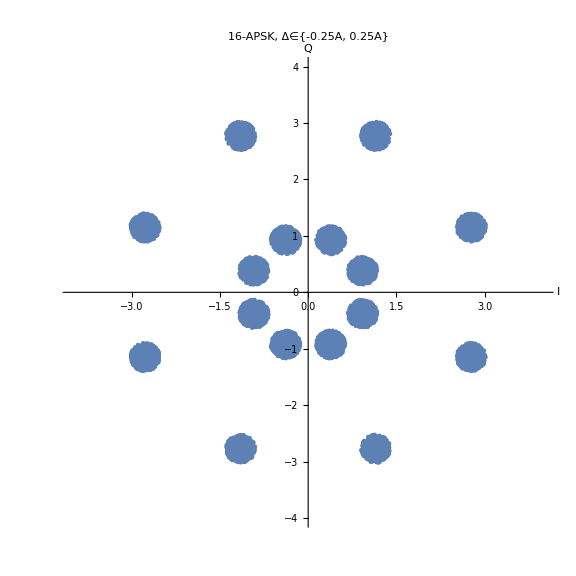

C:\Modulation\Constellation diagram\apsk16n2a0.jpg

```mathematica
apsk16n2a0=ListPlot[Transpose[Module[{n=16000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[Table[{N[k Cos[i 2π]],N[ k Sin[i 2 π]]},{k,1,3,2},{i,1/16,1,1/8}],1],n]];intdata=RandomReal[{-0.25,0.25},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-4,4},{-4,4}},AspectRatio->1,PlotLabel->Style[Framed["16-APSK, Δ∈{-0.25A, 0.25A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\apsk16n2a0.jpg",apsk16n2a0]
```

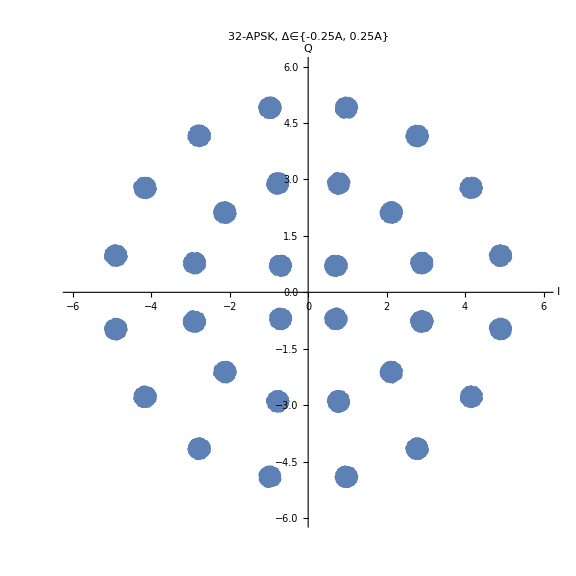

C:\Modulation\Constellation diagram\apsk32n2a0.jpg

```mathematica
apsk32n2a0=ListPlot[Transpose[Module[{n=32000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[{Table[{N[ Cos[i 2π]],N[ Sin[i 2 π]]},{i,1/8,1,1/4}],Table[{N[ 3Cos[i 2π]],N[3Sin[i 2 π]]},{i,1/24,1,1/12}],Table[{N[ 5Cos[i 2π]],N[5Sin[i 2 π]]},{i,1/32,1,1/16}]},1],n]];intdata=RandomReal[{-0.25,0.25},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-6,6},{-6,6}},AspectRatio->1,PlotLabel->Style[Framed["32-APSK, Δ∈{-0.25A, 0.25A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\apsk32n2a0.jpg",apsk32n2a0]
```

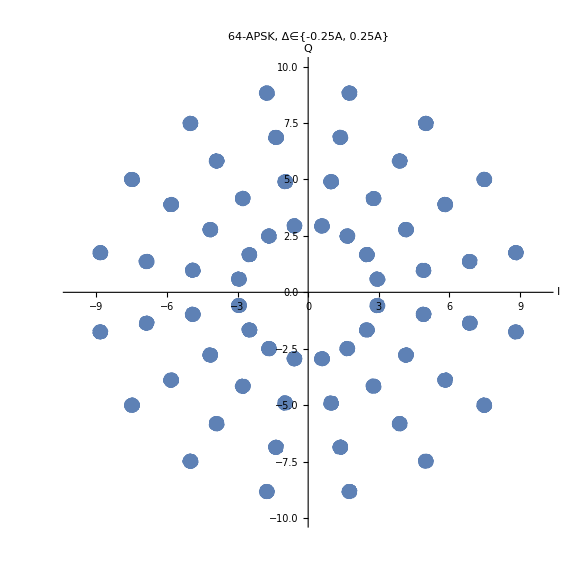

C:\Modulation\Constellation diagram\apsk64n2a0.jpg

```mathematica
apsk64n2a0=ListPlot[Transpose[Module[{n=64000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[Table[{N[ k Cos[i 2π]],N[ k Sin[i 2 π]]},{k,3,9,2},{i,1/32,1,1/16}],1],n]];intdata=RandomReal[{-0.25,0.25},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-10,10},{-10,10}},AspectRatio->1,PlotLabel->Style[Framed["64-APSK, Δ∈{-0.25A, 0.25A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\apsk64n2a0.jpg",apsk64n2a0]
```

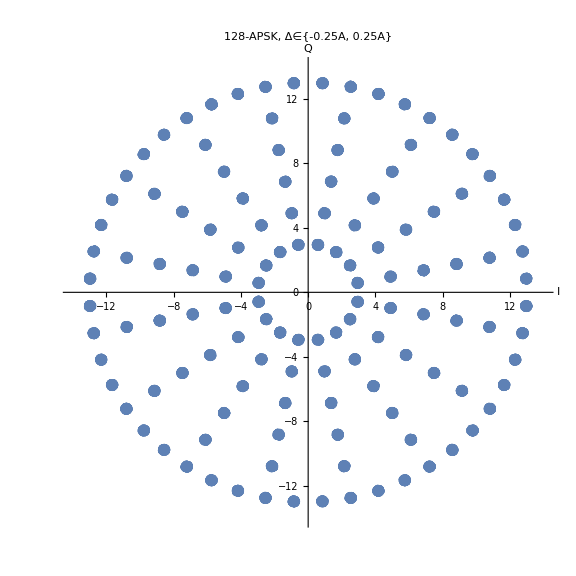

C:\Modulation\Constellation diagram\apsk128n2a0.jpg

```mathematica
apsk128n2a0=ListPlot[Transpose[Module[{n=128000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[{Flatten[Table[{N[k Cos[i 2π]],N[ k Sin[i 2 π]]},{k,3,11,2},{i,1/32,1,1/16}],1],Table[{N[13Cos[i 2π]],N[13Sin[i 2π]]},{i,1/96,1,1/48}]},1],n]];intdata=RandomReal[{-0.25,0.25},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-14,14},{-14,14}},AspectRatio->1,PlotLabel->Style[Framed["128-APSK, Δ∈{-0.25A, 0.25A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\apsk128n2a0.jpg",apsk128n2a0]
```

```mathematica
apsk256n2a0=ListPlot[Transpose[Module[{n=256000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[Table[{N[ k Cos[i 2π]],N[ k Sin[i 2 π]]},{k,5,19,2},{i,1/64,1,1/32}],1],n]];intdata=RandomReal[{-0.25,0.25},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-20,20},{-20,20}},AspectRatio->1,PlotLabel->Style[Framed["256-APSK, Δ∈{-0.25A, 0.25A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\apsk256n2a0.jpg",apsk256n2a0]
```

-Graphics-

C:\Modulation\Constellation diagram\apsk256n2a0.jpg

С шумом Δ∈{-0.5A, 0.5A}

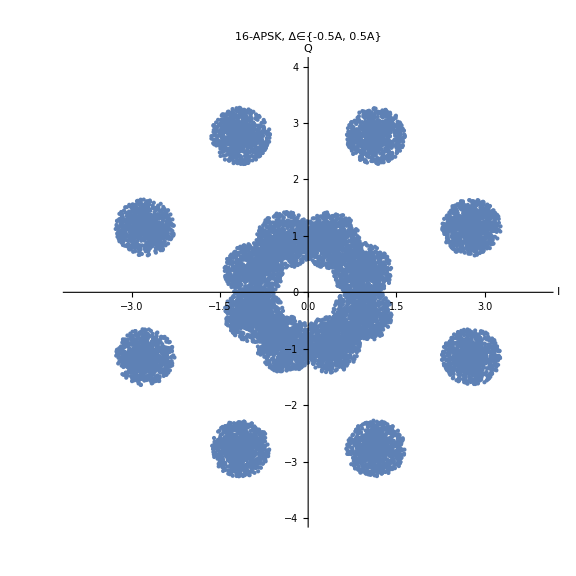

C:\Modulation\Constellation diagram\apsk16n3a0.jpg

```mathematica
apsk16n3a0=ListPlot[Transpose[Module[{n=16000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[Table[{N[k Cos[i 2π]],N[ k Sin[i 2 π]]},{k,1,3,2},{i,1/16,1,1/8}],1],n]];intdata=RandomReal[{-0.5,0.5},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-4,4},{-4,4}},AspectRatio->1,PlotLabel->Style[Framed["16-APSK, Δ∈{-0.5A, 0.5A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\apsk16n3a0.jpg",apsk16n3a0]
```

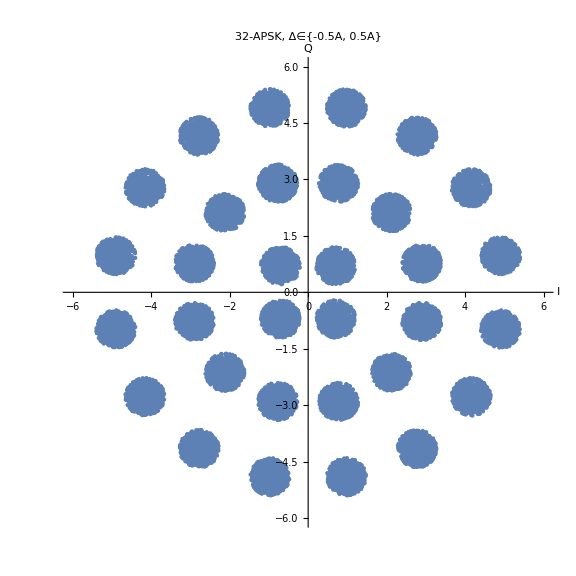

C:\Modulation\Constellation diagram\apsk32n3a0.jpg

```mathematica
apsk32n3a0=ListPlot[Transpose[Module[{n=32000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[{Table[{N[ Cos[i 2π]],N[ Sin[i 2 π]]},{i,1/8,1,1/4}],Table[{N[ 3Cos[i 2π]],N[3Sin[i 2 π]]},{i,1/24,1,1/12}],Table[{N[ 5Cos[i 2π]],N[5Sin[i 2 π]]},{i,1/32,1,1/16}]},1],n]];intdata=RandomReal[{-0.5,0.5},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-6,6},{-6,6}},AspectRatio->1,PlotLabel->Style[Framed["32-APSK, Δ∈{-0.5A, 0.5A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\apsk32n3a0.jpg",apsk32n3a0]
```

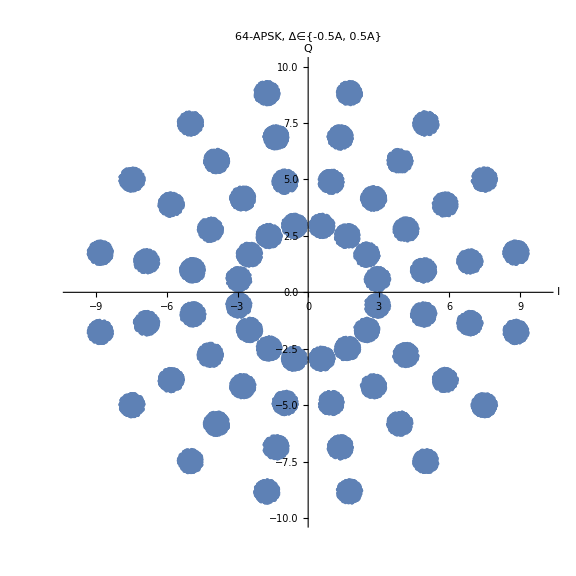

C:\Modulation\Constellation diagram\apsk64n3a0.jpg

```mathematica
apsk64n3a0=ListPlot[Transpose[Module[{n=64000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[Table[{N[ k Cos[i 2π]],N[ k Sin[i 2 π]]},{k,3,9,2},{i,1/32,1,1/16}],1],n]];intdata=RandomReal[{-0.5,0.5},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-10,10},{-10,10}},AspectRatio->1,PlotLabel->Style[Framed["64-APSK, Δ∈{-0.5A, 0.5A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\apsk64n3a0.jpg",apsk64n3a0]
```

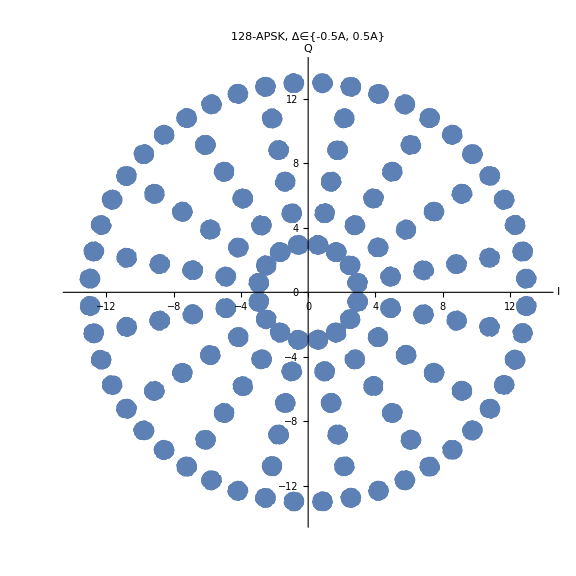

C:\Modulation\Constellation diagram\apsk128n3a0.jpg

```mathematica
apsk128n3a0=ListPlot[Transpose[Module[{n=128000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[{Flatten[Table[{N[k Cos[i 2π]],N[ k Sin[i 2 π]]},{k,3,11,2},{i,1/32,1,1/16}],1],Table[{N[13Cos[i 2π]],N[13Sin[i 2π]]},{i,1/96,1,1/48}]},1],n]];intdata=RandomReal[{-0.5,0.5},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-14,14},{-14,14}},AspectRatio->1,PlotLabel->Style[Framed["128-APSK, Δ∈{-0.5A, 0.5A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\apsk128n3a0.jpg",apsk128n3a0]
```

```mathematica
apsk256n3a0=ListPlot[Transpose[Module[{n=256000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[Table[{N[ k Cos[i 2π]],N[ k Sin[i 2 π]]},{k,5,19,2},{i,1/64,1,1/32}],1],n]];intdata=RandomReal[{-0.5,0.5},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-20,20},{-20,20}},AspectRatio->1,PlotLabel->Style[Framed["256-APSK, Δ∈{-0.5A, 0.5A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\apsk256n3a0.jpg",apsk256n3a0]
```

-Graphics-

C:\Modulation\Constellation diagram\apsk256n3a0.jpg

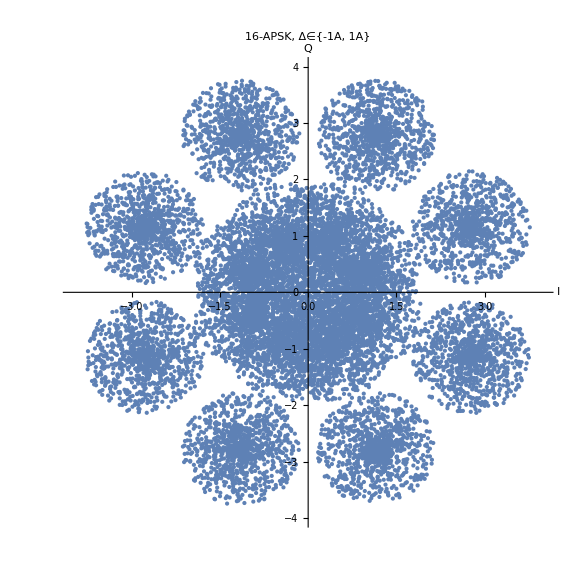

C:\Modulation\Constellation diagram\apsk16n4a0.jpg

```mathematica
apsk16n4a0=ListPlot[Transpose[Module[{n=16000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[Table[{N[k Cos[i 2π]],N[ k Sin[i 2 π]]},{k,1,3,2},{i,1/16,1,1/8}],1],n]];intdata=RandomReal[{-1,1},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-4,4},{-4,4}},AspectRatio->1,PlotLabel->Style[Framed["16-APSK, Δ∈{-1A, 1A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\apsk16n4a0.jpg",apsk16n4a0]
```

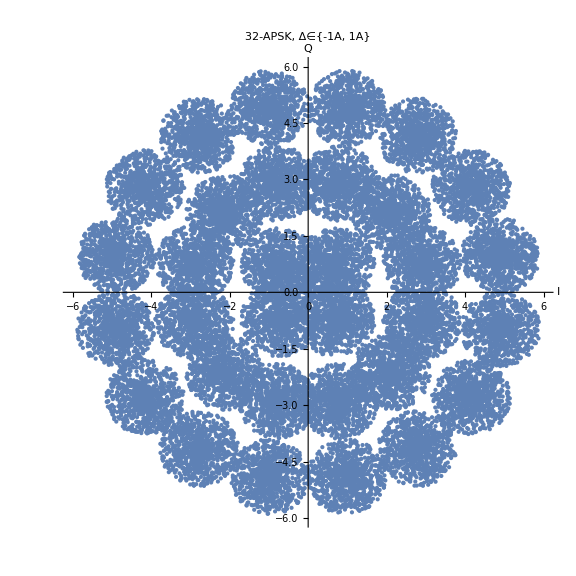

C:\Modulation\Constellation diagram\apsk32n4a0.jpg

```mathematica
apsk32n4a0=ListPlot[Transpose[Module[{n=32000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[{Table[{N[ Cos[i 2π]],N[ Sin[i 2 π]]},{i,1/8,1,1/4}],Table[{N[ 3Cos[i 2π]],N[3Sin[i 2 π]]},{i,1/24,1,1/12}],Table[{N[ 5Cos[i 2π]],N[5Sin[i 2 π]]},{i,1/32,1,1/16}]},1],n]];intdata=RandomReal[{-1,1},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-6,6},{-6,6}},AspectRatio->1,PlotLabel->Style[Framed["32-APSK, Δ∈{-1A, 1A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\apsk32n4a0.jpg",apsk32n4a0]
```

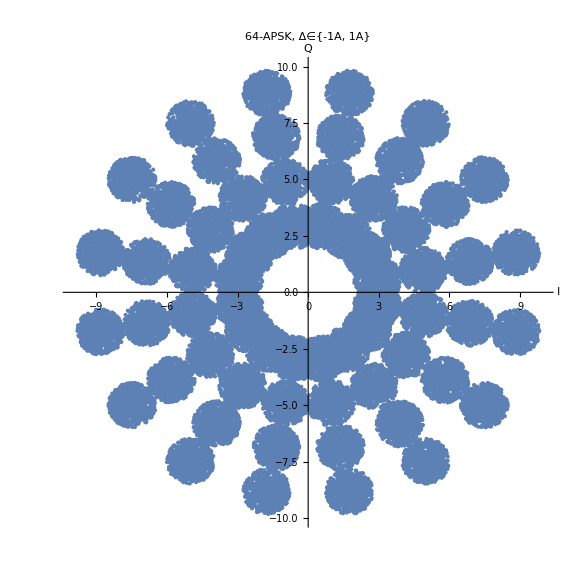

C:\Modulation\Constellation diagram\apsk64n4a0.jpg

```mathematica
apsk64n4a0=ListPlot[Transpose[Module[{n=64000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[Table[{N[ k Cos[i 2π]],N[ k Sin[i 2 π]]},{k,3,9,2},{i,1/32,1,1/16}],1],n]];intdata=RandomReal[{-1,1},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-10,10},{-10,10}},AspectRatio->1,PlotLabel->Style[Framed["64-APSK, Δ∈{-1A, 1A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\apsk64n4a0.jpg",apsk64n4a0]
```

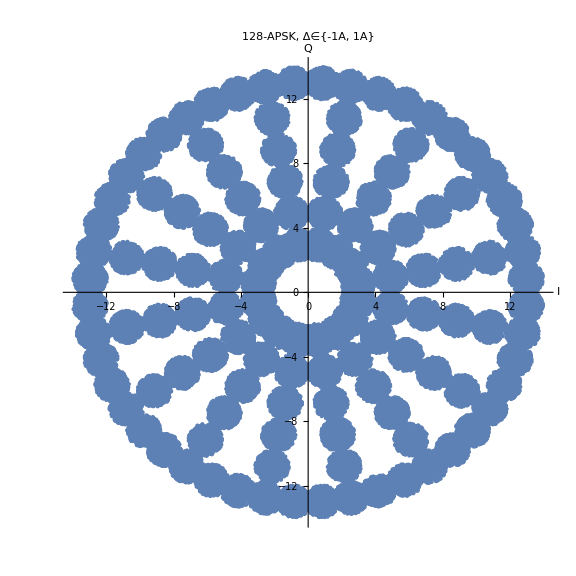

C:\Modulation\Constellation diagram\apsk128n4a0.jpg

```mathematica
apsk128n4a0=ListPlot[Transpose[Module[{n=128000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[{Flatten[Table[{N[k Cos[i 2π]],N[ k Sin[i 2 π]]},{k,3,11,2},{i,1/32,1,1/16}],1],Table[{N[13Cos[i 2π]],N[13Sin[i 2π]]},{i,1/96,1,1/48}]},1],n]];intdata=RandomReal[{-1,1},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-14,14},{-14,14}},AspectRatio->1,PlotLabel->Style[Framed["128-APSK, Δ∈{-1A, 1A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\apsk128n4a0.jpg",apsk128n4a0]
```

```mathematica
apsk256n4a0=ListPlot[Transpose[Module[{n=256000,data={},intdata={},andata={}},data=Transpose[RandomChoice[Flatten[Table[{N[ k Cos[i 2π]],N[ k Sin[i 2 π]]},{k,5,19,2},{i,1/64,1,1/32}],1],n]];intdata=RandomReal[{-1,1},n];andata=RandomReal[{-π,π},n];data=data+Transpose[Table[{intdata[[k]]Cos[andata[[k]]],intdata[[k]]Sin[andata[[k]]]},{k,1,n}]];data]],PlotStyle->PointSize[Tiny],PlotRange->{{-20,20},{-20,20}},AspectRatio->1,PlotLabel->Style[Framed["256-APSK, Δ∈{-1A, 1A}"],32],AxesStyle->Arrowheads[{-0.05,0.05}],AxesLabel->{Style["I",Large,Bold],Style["Q",Large,Bold]},ImageSize->Large]
Export["C:\\Modulation\\Constellation diagram\\apsk256n4a0.jpg",apsk256n4a0]
```

-Graphics-

C:\Modulation\Constellation diagram\apsk256n4a0.jpg